```mathematica
(* Clear content *)
ClearAll
```

ClearAll

```mathematica
(* Define the wavelenghts and corresponding summand *)
lambdai[i_]=λ+(i-1)*δ
lambdaj[i_,j_]=λ+(j-1)*δ
summand[i_,j_]=FullSimplify[(lambdai[i]*lambdaj[i,j]/(lambdai[i]-lambdaj[i,j]))^2]
```

(-1+i) δ+λ

(-1+j) δ+λ

(((-1+i) δ+λ)^2 ((-1+j) δ+λ)^2)/((i-j)^2 δ^2)

```mathematica
(* Alternative, simplified form of the summand *)
summandFull[i_,j_]=1/(i-j)^2*(1+Δ*(i-1))^2*(1+Δ*(j-1))^2
```

((1+(-1+i) Δ)^2 (1+(-1+j) Δ)^2)/(i-j)^2

```mathematica
(* Calculate the inner sum over i. NN is the total number of wavelengths consider *)
summedInner[i_]=FullSimplify[Sum[summandFull[i,j],{j,i+1,NN}]]
```

1/6 (1+(-1+i) Δ)^2 (6 Δ (2 EulerGamma+(2 EulerGamma (-1+i)-i+NN) Δ)+(π+(-1+i) π Δ)^2+12 Δ (1+(-1+i) Δ) PolyGamma[0,1-i+NN]-6 (1+(-1+i) Δ)^2 PolyGamma[1,1-i+NN])

```mathematica
(* Calculate the outer sum over j *)
Sum[summedInner[i],{i,1,NN}]-summedInner[NN]
```

-1/6 (1+(-1+NN) Δ)^2 (-12 EulerGamma Δ (1+(-1+NN) Δ)-π^2 (1+(-1+NN) Δ)^2+6 Δ (2 EulerGamma+2 EulerGamma (-1+NN) Δ)+(π+(-1+NN) π Δ)^2)+1/360 (-360 EulerGamma+60 NN π^2+720 EulerGamma Δ-720 EulerGamma NN Δ-120 NN π^2 Δ+120 NN^2 π^2 Δ-360 EulerGamma Δ^2+1080 EulerGamma NN Δ^2+360 NN^2 Δ^2-1080 EulerGamma NN^2 Δ^2+60 NN π^2 Δ^2-180 NN^2 π^2 Δ^2+120 NN^3 π^2 Δ^2-360 EulerGamma NN Δ^3-360 NN^2 Δ^3+1080 EulerGamma NN^2 Δ^3+360 NN^3 Δ^3-720 EulerGamma NN^3 Δ^3+60 NN^2 π^2 Δ^3-120 NN^3 π^2 Δ^3+60 NN^4 π^2 Δ^3+12 EulerGamma Δ^4+57 NN^2 Δ^4-180 EulerGamma NN^2 Δ^4-186 NN^3 Δ^4+360 EulerGamma NN^3 Δ^4+117 NN^4 Δ^4-180 EulerGamma NN^4 Δ^4-2 NN π^2 Δ^4+20 NN^3 π^2 Δ^4-30 NN^4 π^2 Δ^4+12 NN^5 π^2 Δ^4-360 PolyGamma[0,1+NN]+720 Δ PolyGamma[0,1+NN]-720 NN Δ PolyGamma[0,1+NN]-360 Δ^2 PolyGamma[0,1+NN]+1080 NN Δ^2 PolyGamma[0,1+NN]-1080 NN^2 Δ^2 PolyGamma[0,1+NN]-360 NN Δ^3 PolyGamma[0,1+NN]+1080 NN^2 Δ^3 PolyGamma[0,1+NN]-720 NN^3 Δ^3 PolyGamma[0,1+NN]+12 Δ^4 PolyGamma[0,1+NN]-180 NN^2 Δ^4 PolyGamma[0,1+NN]+360 NN^3 Δ^4 PolyGamma[0,1+NN]-180 NN^4 Δ^4 PolyGamma[0,1+NN]-360 NN PolyGamma[1,1+NN]+720 NN Δ PolyGamma[1,1+NN]-720 NN^2 Δ PolyGamma[1,1+NN]-360 NN Δ^2 PolyGamma[1,1+NN]+1080 NN^2 Δ^2 PolyGamma[1,1+NN]-720 NN^3 Δ^2 PolyGamma[1,1+NN]-360 NN^2 Δ^3 PolyGamma[1,1+NN]+720 NN^3 Δ^3 PolyGamma[1,1+NN]-360 NN^4 Δ^3 PolyGamma[1,1+NN]+12 NN Δ^4 PolyGamma[1,1+NN]-120 NN^3 Δ^4 PolyGamma[1,1+NN]+180 NN^4 Δ^4 PolyGamma[1,1+NN]-72 NN^5 Δ^4 PolyGamma[1,1+NN])

```mathematica
(* Simplify this expression *)
sumTot = FullSimplify[%]
```

1/360 (12 EulerGamma (-30-60 (-1+NN) Δ-30 (1+3 (-1+NN) NN) Δ^2-30 (-1+NN) NN (-1+2 NN) Δ^3+(1-15 (-1+NN)^2 NN^2) Δ^4)+NN (3 NN Δ^2 (120+120 (-1+NN) Δ+(19+NN (-62+39 NN)) Δ^2)+2 π^2 (30+(-1+NN) Δ (60+Δ (-30+60 NN+30 (-1+NN) NN Δ+(1+NN-9 NN^2+6 NN^3) Δ^2))))-12 (30+60 (-1+NN) Δ+30 (1+3 (-1+NN) NN) Δ^2+30 (-1+NN) NN (-1+2 NN) Δ^3+(-1+15 (-1+NN)^2 NN^2) Δ^4) PolyGamma[0,1+NN]-12 NN (30+(-1+NN) Δ (60+Δ (-30+60 NN+30 (-1+NN) NN Δ+(1+NN-9 NN^2+6 NN^3) Δ^2))) PolyGamma[1,1+NN])

```mathematica
(* Use the ToMatlab extension to write this expression to Matlab *)
<<ToMatlab`
sumTot//ToMatlab
```

(1/360).*(12.*EulerGamma.*((-30)+(-60).*((-1)+NN).*Δ+(-30).*(1+3.* ...
  ((-1)+NN).*NN).*Δ.^2+(-30).*((-1)+NN).*NN.*((-1)+2.*NN).*Δ.^3+(1+( ...
  -15).*((-1)+NN).^2.*NN.^2).*Δ.^4)+NN.*(3.*NN.*Δ.^2.*(120+120.*(( ...
  -1)+NN).*Δ+(19+NN.*((-62)+39.*NN)).*Δ.^2)+2.*pi.^2.*(30+((-1)+NN) ...
  .*Δ.*(60+Δ.*((-30)+60.*NN+30.*((-1)+NN).*NN.*Δ+(1+NN+(-9).*NN.^2+ ...
  6.*NN.^3).*Δ.^2))))+(-12).*(30+60.*((-1)+NN).*Δ+30.*(1+3.*((-1)+ ...
  NN).*NN).*Δ.^2+30.*((-1)+NN).*NN.*((-1)+2.*NN).*Δ.^3+((-1)+15.*(( ...
  -1)+NN).^2.*NN.^2).*Δ.^4).*PolyGamma(0,1+NN)+(-12).*NN.*(30+((-1)+ ...
  NN).*Δ.*(60+Δ.*((-30)+60.*NN+30.*((-1)+NN).*NN.*Δ+(1+NN+(-9).* ...
  NN.^2+6.*NN.^3).*Δ.^2))).*PolyGamma(1,1+NN));

```mathematica
(* Change Δ to Range / (N-1) *)
variableChange=FullSimplify[sumTot/.{Δ->R/(NN-1)}]
```

1/360 (NN ((3 NN R^2 (120+R (120+((19+NN (-62+39 NN)) R)/(-1+NN)^2)))/(-1+NN)^2+2 π^2 (30+R (60+(R (-30+60 NN+30 NN R+((1+NN-9 NN^2+6 NN^3) R^2)/(-1+NN)^2))/(-1+NN))))+12 EulerGamma (-30+R (-60+(R (-30+R^2+30 NN (5+R)-15 NN^4 (6+R (4+R))+30 NN^3 (9+R (5+R))-15 NN^2 (20+R (8+R))))/(-1+NN)^4))-12 (30+R (60+(R (30 (-1+NN)^2 (1+3 (-1+NN) NN)+30 (-1+NN)^2 NN (-1+2 NN) R+(-1+15 (-1+NN)^2 NN^2) R^2))/(-1+NN)^4)) PolyGamma[0,1+NN]-12 NN (30+R (60+(R (-30+60 NN+30 NN R+((1+NN-9 NN^2+6 NN^3) R^2)/(-1+NN)^2))/(-1+NN))) PolyGamma[1,1+NN])

```mathematica
(* Now define the Sum as shown in the article (Eq. 30) *)
Sfunction=FullSimplify[variableChange/(NN^2*R^2)]
```

1/(360 NN^2 R^2)(NN ((3 NN R^2 (120+R (120+((19+NN (-62+39 NN)) R)/(-1+NN)^2)))/(-1+NN)^2+2 π^2 (30+R (60+(R (-30+60 NN+30 NN R+((1+NN-9 NN^2+6 NN^3) R^2)/(-1+NN)^2))/(-1+NN))))+12 EulerGamma (-30+R (-60+(R (-30+R^2+30 NN (5+R)-15 NN^4 (6+R (4+R))+30 NN^3 (9+R (5+R))-15 NN^2 (20+R (8+R))))/(-1+NN)^4))-12 (30+R (60+(R (30 (-1+NN)^2 (1+3 (-1+NN) NN)+30 (-1+NN)^2 NN (-1+2 NN) R+(-1+15 (-1+NN)^2 NN^2) R^2))/(-1+NN)^4)) PolyGamma[0,1+NN]-12 NN (30+R (60+(R (-30+60 NN+30 NN R+((1+NN-9 NN^2+6 NN^3) R^2)/(-1+NN)^2))/(-1+NN))) PolyGamma[1,1+NN])

```mathematica
(* To Matlab again *)
Sfunction//ToMatlab
```

(1/360).*NN.^(-2).*R.^(-2).*(NN.*(3.*((-1)+NN).^(-2).*NN.*R.^2.*( ...
  120+R.*(120+((-1)+NN).^(-2).*(19+NN.*((-62)+39.*NN)).*R))+2.* ...
  pi.^2.*(30+R.*(60+((-1)+NN).^(-1).*R.*((-30)+60.*NN+30.*NN.*R+(( ...
  -1)+NN).^(-2).*(1+NN+(-9).*NN.^2+6.*NN.^3).*R.^2))))+12.* ...
  EulerGamma.*((-30)+R.*((-60)+((-1)+NN).^(-4).*R.*((-30)+R.^2+30.* ...
  NN.*(5+R)+(-15).*NN.^4.*(6+R.*(4+R))+30.*NN.^3.*(9+R.*(5+R))+(-15) ...
  .*NN.^2.*(20+R.*(8+R)))))+(-12).*(30+R.*(60+((-1)+NN).^(-4).*R.*( ...
  30.*((-1)+NN).^2.*(1+3.*((-1)+NN).*NN)+30.*((-1)+NN).^2.*NN.*((-1) ...
  +2.*NN).*R+((-1)+15.*((-1)+NN).^2.*NN.^2).*R.^2))).*PolyGamma(0,1+ ...
  NN)+(-12).*NN.*(30+R.*(60+((-1)+NN).^(-1).*R.*((-30)+60.*NN+30.* ...
  NN.*R+((-1)+NN).^(-2).*(1+NN+(-9).*NN.^2+6.*NN.^3).*R.^2))).* ...
  PolyGamma(1,1+NN));

```mathematica
(* Asymptotic analysis as N is large *)
Series[Sfunction,{NN,∞,1}]
```

(π^2 (5+10 R+10 R^2+5 R^3+R^4))/(30 R^2 NN)+O[1/NN]^2

```mathematica
(* Same idea *)
infAsymptote=FullSimplify[Normal[Series[Sfunction,{NN,∞,1}]]]
```

(π^2 (5+R (10+R (10+R (5+R)))))/(30 NN R^2)

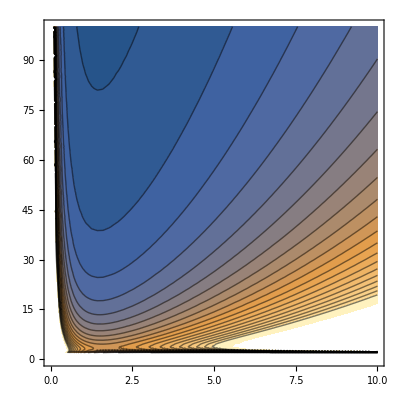

```mathematica
(* Contour plot of the Sum (Figure 4 in article) *)
ContourPlot[Sfunction,{R,0.001,10},{NN,2,100},Contours->20,PlotRange->Automatic]
```

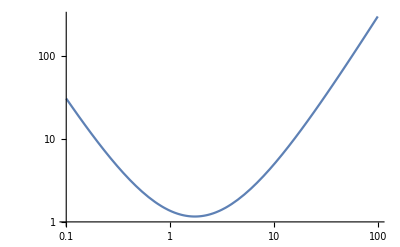

```mathematica
(* Slice at N = 3 *)
LogLogPlot[Sfunction/.{NN->3},{R,0.1,100}]
```

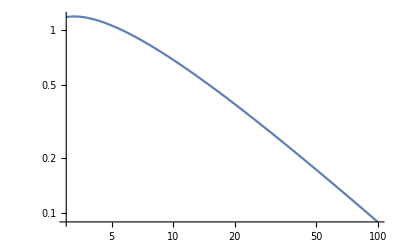

```mathematica
(* Slice at R -> 1.4587 (optimal R for large N) *)
LogLogPlot[Sfunction/.{R->1.4587},{NN,3,100}]
```

```mathematica
(* Find the optimal R for N=3 *)
dR = FullSimplify[D[Sfunction/.{NN->3},R]]
```

((-3+R^2) (3+R (3+R)))/(18 R^3)

```mathematica
N[Solve[dR==0,R]]
```

{{R→-1.73205},{R→1.73205},{R→-1.5-0.866025 ⅈ},{R→-1.5+0.866025 ⅈ}}

```mathematica
(* Find the optimal R for large N *)
(* First define the function of interest *)
fR[R_]=1/R^2*(R^4/5+R^3+2*R^2+2*R+1)
```

(1+2 R+2 R^2+R^3+R^4/5)/R^2

```mathematica
(* Then compute its derivative and solve the point for which the derivative is 0. Only a single positive real rool *)
N[Solve[D[fR[R],R]==0]]
```

{{R→-1.81987},{R→1.45897},{R→-1.06955-0.859767 ⅈ},{R→-1.06955+0.859767 ⅈ}}